```mathematica
NN = 3;
```

```mathematica
m0[m_] := m

m1[m_] := m ⅇ^(2 π ⅈ / NN)

m2[m_] := m ⅇ^(4 π ⅈ / NN)

σ0[m_] := ⅇ^(1/NN Log[ 1 + m^NN])Piecewise[  {{  ⅇ^(2 π ⅈ / NN),Arg[m] ≥ π /3 } , { ⅇ^(-2 π ⅈ / NN),  Arg[m] ≤ - π /3}}, 1 ]

σ1[m_] := σ0[m] ⅇ^(2 π ⅈ / NN)


σ2[m_] := σ0[m] ⅇ^(4 π ⅈ / NN)

W0[m_] :=  (- 1)/(2π)( NN σ0[m] + ∑_(j=0)^(NN-1) m ⅇ^(2 π ⅈ j / NN) Log[ σ0[m] - m ⅇ^(2 π ⅈ  j/ NN)])

W1[m_] :=  (- 1)/(2π)( NN σ1[m] + ∑_(j=0)^(NN-1) m ⅇ^(2 π ⅈ j / NN) Log[ σ1[m] - m ⅇ^(2 π ⅈ  j/ NN)])

W2[m_] :=  (- 1)/(2π)( NN σ2[m] + ∑_(j=0)^(NN-1) m ⅇ^(2 π ⅈ j / NN) Log[ σ2[m] - m ⅇ^(2π ⅈ  j/ NN)])
```

```mathematica
CMS[m_] :=  Piecewise[ {{ (ⅇ^(2 π ⅈ / NN)( ⅇ^(2 π ⅈ / NN) - 1 ) W2[m] + ⅈ m1[m])/(m1[m] - m0[m]), Abs[Arg[m]] ≥ π/2}}, (( ⅇ^(2 π ⅈ / NN) - 1 ) W0[m] + ⅈ m0[m])/(m1[m] - m0[m])]
```

```mathematica
top0[m_] := ( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m
top1[m_] := ( 1  - ⅇ^(- 2 π ⅈ / NN) ) W1[m]  + ⅈ (m1[m] - m0[m])  + ⅈ m2[m]
top2[m_] := ⅇ^(2 π ⅈ / NN)( ⅇ^(2 π ⅈ / NN) - 1 ) W2[m] + ⅈ m1[m]
quark1[m_]   :=  m1[m]  -  m0[m]
quark2[m_]   :=  m2[m]  -  m0[m]
quark21[m_] :=  m2[m]  -  m1[m]
```

```mathematica
M[m_] :=  ( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m2[m]
Q10[m_] := ⅈ  ( m1[m] - m0[m] )
Q12[m_] := ⅈ (  m1[m] - m2[m] )
Q02[m_] := ⅈ (  m0[m] - m2[m]  )
```

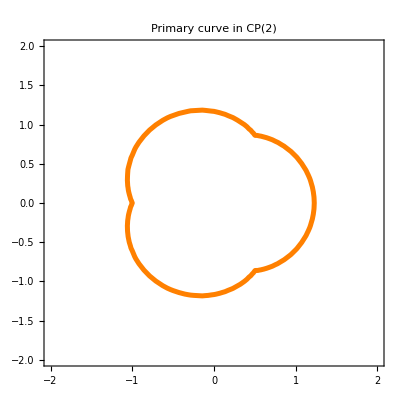

```mathematica
ContourPlot[    Evaluate[   Re[  CMS[ x + ⅈ y ]] == 0], 
                             { x , -2, 2}, { y, -2, 2 },
                             ContourStyle->
                          { Directive[ Thickness[0.009], Orange ]  },
                             PlotLabel-> Style["Primary curve in CP(2)",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

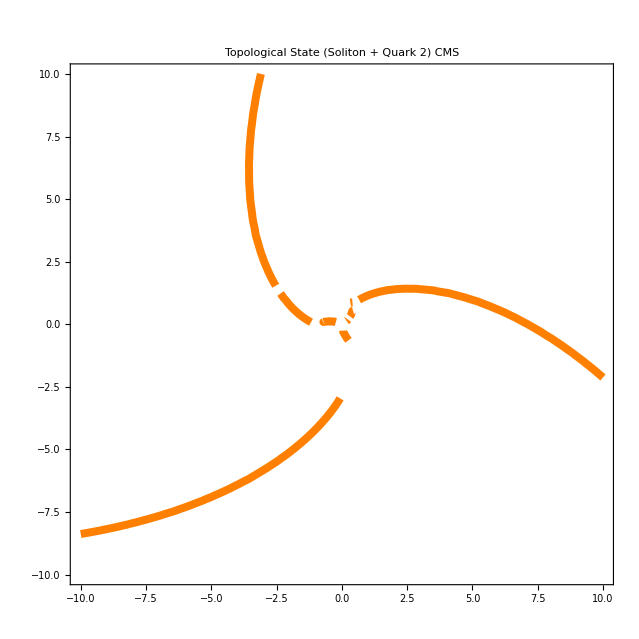

```mathematica
distance = 10.0;
ContourPlot[    Evaluate[   { Im[  top0[x + ⅈ y]/(ⅈ quark2[x + ⅈ y])] == 0 } ], 
                             { x , -distance, distance}, { y, -distance, distance },
                             ContourStyle->
                          { Directive[ Thickness[0.009], Orange ] },
                             PlotLabel-> Style["Topological State (Soliton + Quark 2) CMS",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

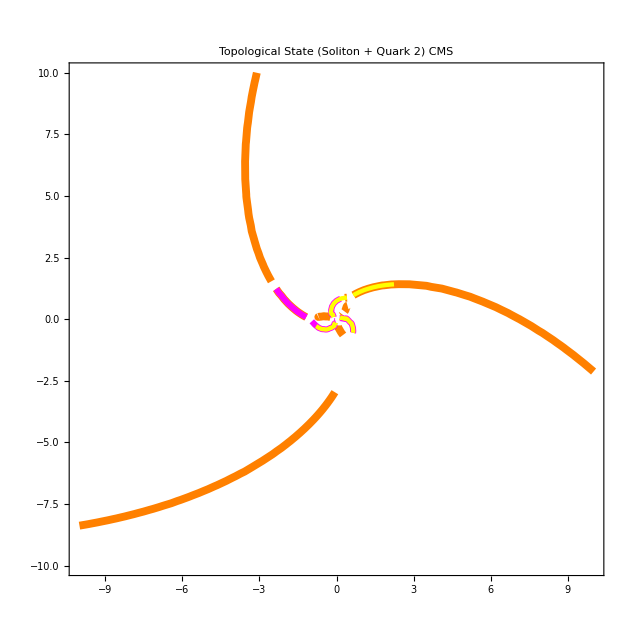

```mathematica
ContourPlot[    Evaluate[  { Im[  top0[x + ⅈ y]/(ⅈ quark2[x + ⅈ y])] == 0, Im[  top1[x + ⅈ y]/(ⅈ quark2[x + ⅈ y])] == 0, Im[  top2[x + ⅈ y]/(ⅈ quark2[x + ⅈ y])] == 0} ], 
                             { x , -distance, distance}, { y, -distance, distance },
                             ContourStyle->
                          { Directive[ Thickness[0.009], Orange ], Directive[ Thickness[0.007], Magenta], Directive[ Thickness[0.005], Yellow]  },
                             PlotLabel-> Style["Topological State (Soliton + Quark 2) CMS",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

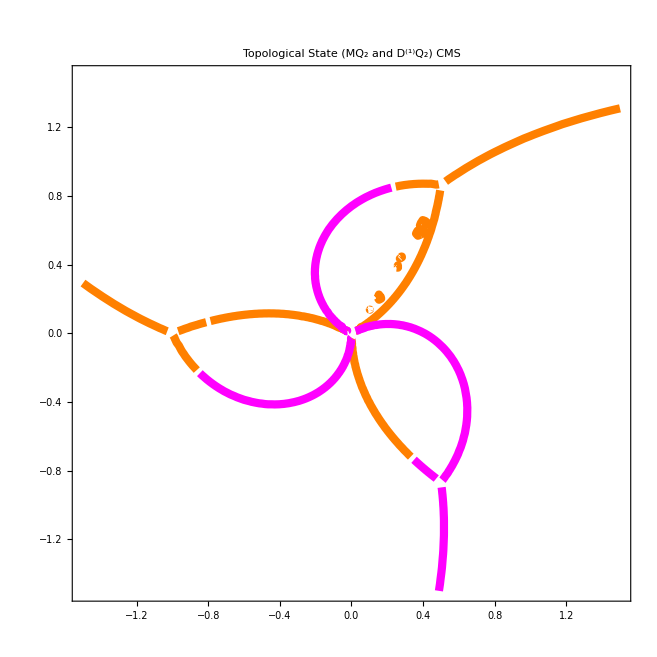

```mathematica
distance = 1.5;
ContourPlot[    Evaluate[  { Im[  top0[x + ⅈ y]/(ⅈ quark2[x + ⅈ y])] == 0,  Im[  (top0[x + ⅈ y] + ⅈ quark1[x + ⅈ y])/(ⅈ quark2[x + ⅈ y])] == 0} ], 
                             { x , -distance, distance}, { y, -distance, distance },
                             ContourStyle->
                          { Directive[ Thickness[0.009], Orange ], Directive[ Thickness[0.009],  Magenta ] },
                             PlotLabel-> Style["Topological State (MQ_2 and D^(1)Q_2) CMS",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

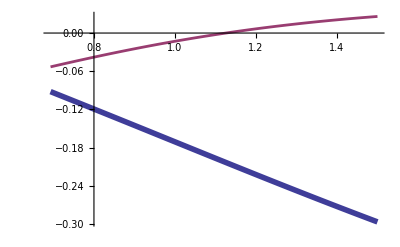

```mathematica
v = 1.2;
Plot [ { Re[top0[x + ⅈ v]/(ⅈ quark2[x + ⅈ v])],Im[top0[x + ⅈ v]/(ⅈ quark2[x + ⅈ v])]}, { x, v Cot[π/NN], 1.5 },PlotStyle->{Thickness[0.01],Thickness[0.005]} ]
```

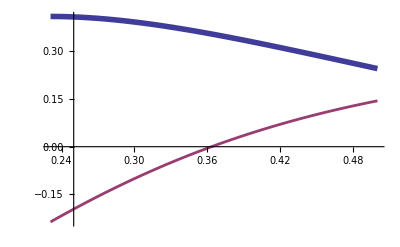

```mathematica
v = 0.4;
Plot [  { Re[top0[x + ⅈ v]/(ⅈ quark2[x + ⅈ v])],Im[top0[x + ⅈ v]/(ⅈ quark2[x + ⅈ v])]}, { x, v Cot[π/NN], 0.5 },PlotStyle->{Thickness[0.01],Thickness[0.005]} ]
```

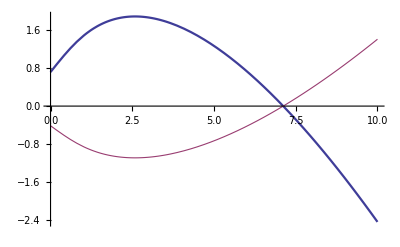

```mathematica
v=0;
distance = 10;
Plot[ { Re[  top0[x + ⅈ v] + ⅈ quark2[x + ⅈ v] ],    Im[  top0[x + ⅈ v] + ⅈ quark2[x + ⅈ v] ] }, { x, 0, distance },
           PlotStyle->{ Directive[ Thickness[0.004]],  Directive[ Thickness[0.002]] } ]
```

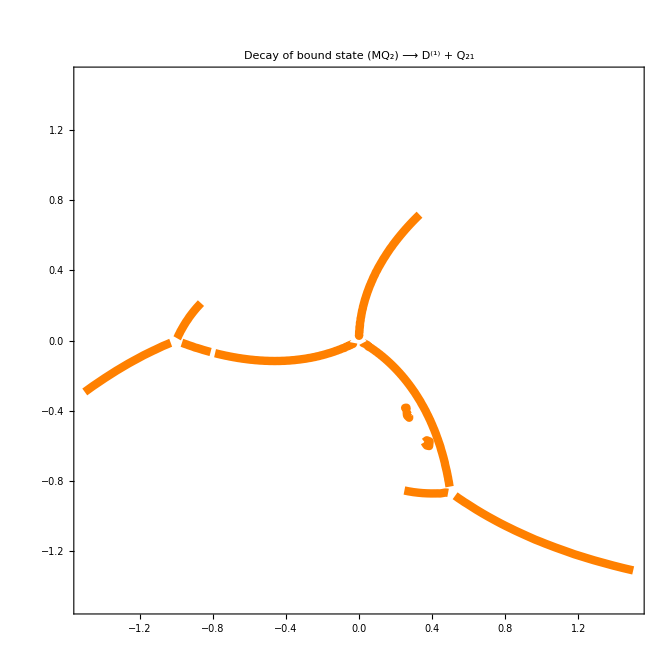

```mathematica
distance = 1.5;
ContourPlot[    Evaluate[  {  Im[  (top0[x + ⅈ y] + ⅈ quark1[x + ⅈ y])/(ⅈ quark21[x + ⅈ y])] == 0 } ], 
                             { x , -distance, distance}, { y, -distance, distance },
                             ContourStyle->
                          { Directive[ Thickness[0.009], Orange ] },
                             PlotLabel-> Style["Decay of bound state  (MQ_2)  ⟶  D^(1) + Q_21",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

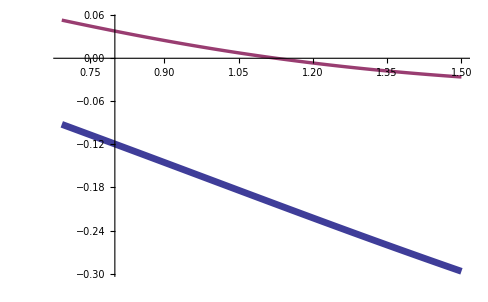

```mathematica
v=-1.2;
Plot[ { Re[  (top0[x + ⅈ v] + ⅈ  quark1[x + ⅈ v])/(ⅈ quark21[x + ⅈ v])],Im[  (top0[x + ⅈ v] + ⅈ  quark1[x + ⅈ v])/(ⅈ quark21[x + ⅈ v])]} , { x, Abs[v] Cot[π/NN], 1.5} ,
          PlotStyle->{Thickness[0.01],Thickness[0.005]}]
```

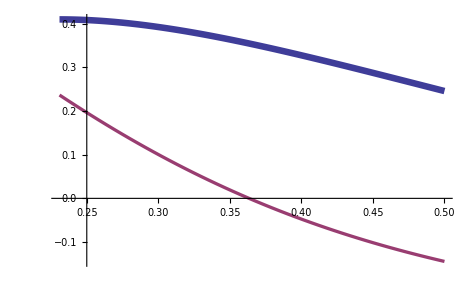

```mathematica
v= -0.4;
Plot[ { Re[  (top0[x + ⅈ v] + ⅈ  quark1[x + ⅈ v])/(ⅈ quark21[x + ⅈ v])],Im[  (top0[x + ⅈ v] + ⅈ  quark1[x + ⅈ v])/(ⅈ quark21[x + ⅈ v])]} , { x, Abs[v] Cot[π/NN], 0.5} ,
          PlotStyle->{Thickness[0.01],Thickness[0.005]}]
```

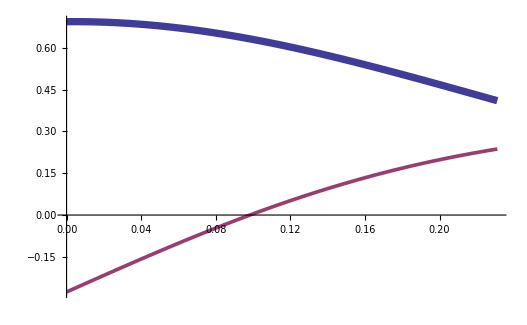

```mathematica
v= 0.4;
Plot[ { Re[  (top0[x + ⅈ v] + ⅈ  quark1[x + ⅈ v])/(ⅈ quark21[x + ⅈ v])],Im[  (top0[x + ⅈ v] + ⅈ  quark1[x + ⅈ v])/(ⅈ quark21[x + ⅈ v])]} , { x, 0,Abs[v] Cot[π/NN]} ,
          PlotStyle->{Thickness[0.01],Thickness[0.005]}]
```

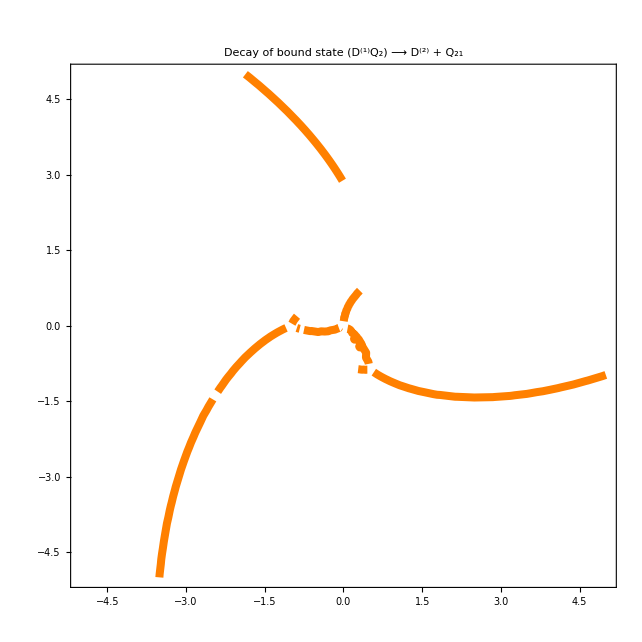

```mathematica
distance=5;
ContourPlot[    Evaluate[  {  Im[  (top0[x + ⅈ y] + ⅈ quark1[x + ⅈ y])/(ⅈ quark21[x + ⅈ y])] == 0 } ], 
                             { x , -distance, distance}, { y, -distance, distance },
                             ContourStyle->
                          { Directive[ Thickness[0.009], Orange ] },
                             PlotLabel-> Style["Decay of bound state  (D^(1)Q_2) ⟶  D^(2)  +  Q_21",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

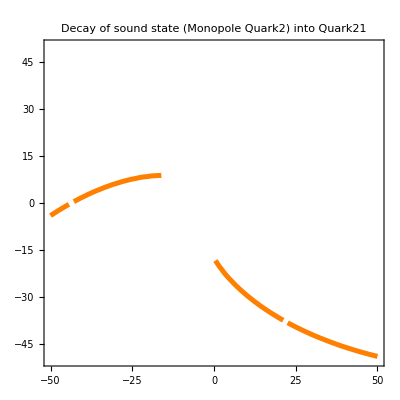

```mathematica
distance=50;
ContourPlot[    Evaluate[  {  Im[  (top0[x + ⅈ y] + ⅈ 2quark1[x + ⅈ y])/(ⅈ quark21[x + ⅈ y])] == 0 } ], 
                             { x , -distance, distance}, { y, -distance, distance },
                             ContourStyle->
                          { Directive[ Thickness[0.009], Orange ] },
                             PlotLabel-> Style["Decay of sound state (Monopole Quark2) into Quark21",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

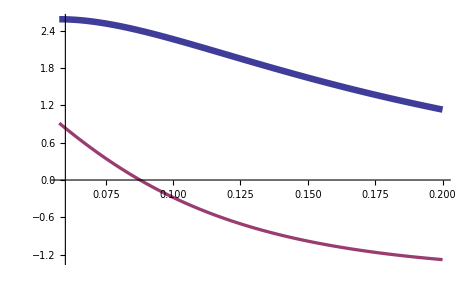

```mathematica
v = -0.1;
Plot[ { Re[  (top0[x + ⅈ v] + ⅈ  2quark1[x + ⅈ v])/(ⅈ quark21[x + ⅈ v])],Im[  (top0[x + ⅈ v] + ⅈ  2quark1[x + ⅈ v])/(ⅈ quark21[x + ⅈ v])]} , { x, Abs[v] Cot[π/NN],0.2} ,
          PlotStyle->{Thickness[0.01],Thickness[0.005]}]
```

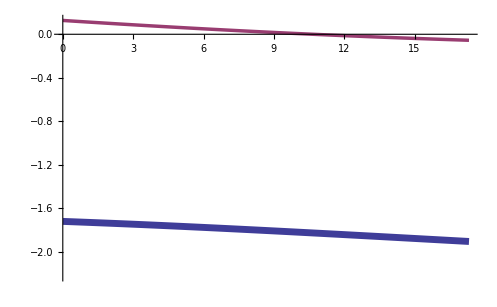

```mathematica
v= -30;
Plot[ { Re[  (top0[x + ⅈ v] + ⅈ  2quark1[x + ⅈ v])/(ⅈ quark21[x + ⅈ v])],Im[  (top0[x + ⅈ v] + ⅈ  2quark1[x + ⅈ v])/(ⅈ quark21[x + ⅈ v])]} , { x, 0,Abs[v] Cot[π/NN]} ,
          PlotStyle->{Thickness[0.01],Thickness[0.005]}]
```

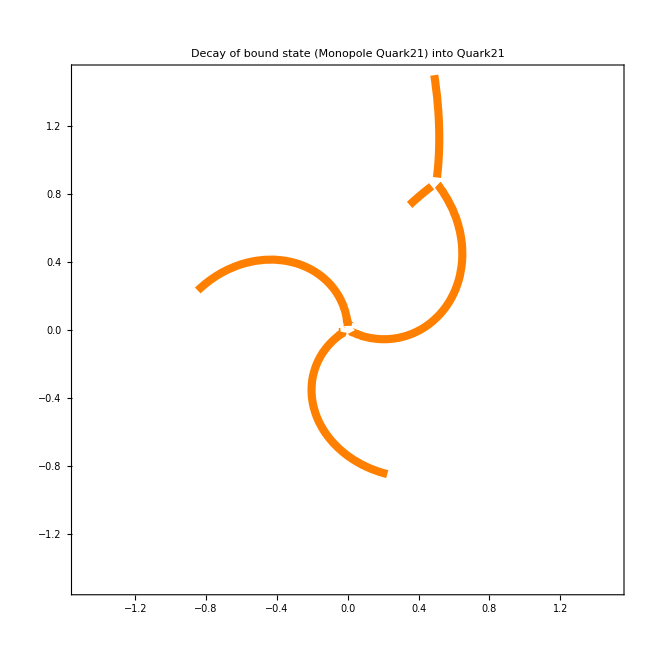

```mathematica
distance = 1.5;
ContourPlot[    Evaluate[  {  Im[  top0[x + ⅈ y]/(ⅈ quark21[x + ⅈ y])] == 0 } ], 
                             { x , -distance, distance}, { y, -distance, distance },
                             ContourStyle->
                          { Directive[ Thickness[0.009], Orange ] },
                             PlotLabel-> Style["Decay of bound state (Monopole Quark21) into Quark21",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

```mathematica
mc[a_]:= ⅇ^(1/NN Log[a])
mz[a_,b_] := ⅇ^(1/NN ⅈ Arg[a + ⅈ b]) Exp[ √(a^2 + b^2)]
```

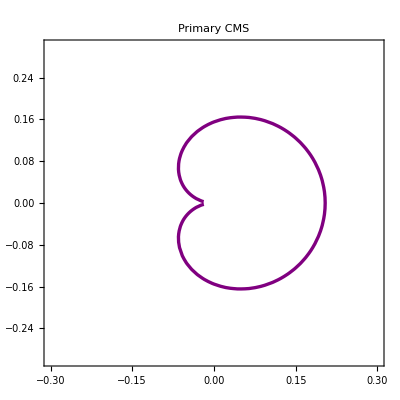

```mathematica
distance = 0.3;
ContourPlot[    Evaluate[  {  Im[  top0[mz[x,y]]/(ⅈ quark1[mz[x,y]])] == 0 } ], 
                             { x , -distance, distance},{y, -distance,distance},
                             ContourStyle->
                          { Directive[ Thickness[0.006], Purple]  },
                             PlotLabel-> Style["Primary CMS",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

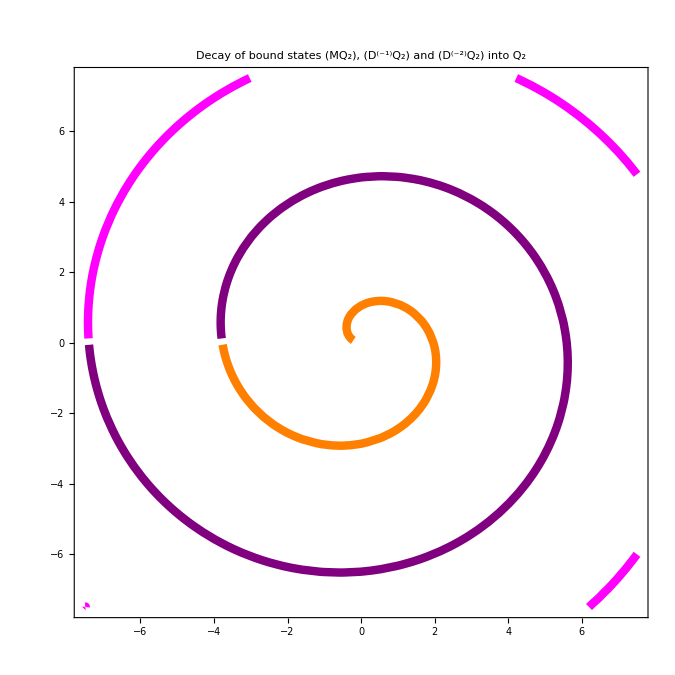

```mathematica
distance = 7.5;
ContourPlot[    Evaluate[  {  Im[  (top0[mz[x,y]] + ⅈ  0 quark1[mz[x,y]])/(ⅈ quark2[mz[x,y]])] == 0,
                                                    Im[  (top0[mz[x,y]] + ⅈ  ( -1) quark1[mz[x,y]])/(ⅈ quark2[mz[x,y]])] == 0,
                                                     Im[  (top0[mz[x,y]] + ⅈ  ( -2) quark1[mz[x,y]])/(ⅈ quark2[mz[x,y]])] == 0  } ], 
                             { x , -distance, distance},{y, -distance,distance},
                             ContourStyle->
                          { Directive[ Thickness[0.009], Orange ], Directive[ Thickness[0.009], Purple ],  Directive[ Thickness[0.009], Magenta]  },
                             PlotLabel-> Style["Decay of bound states (MQ_2), (D^(-1)Q_2) and (D^(-2)Q_2) into Q_2",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

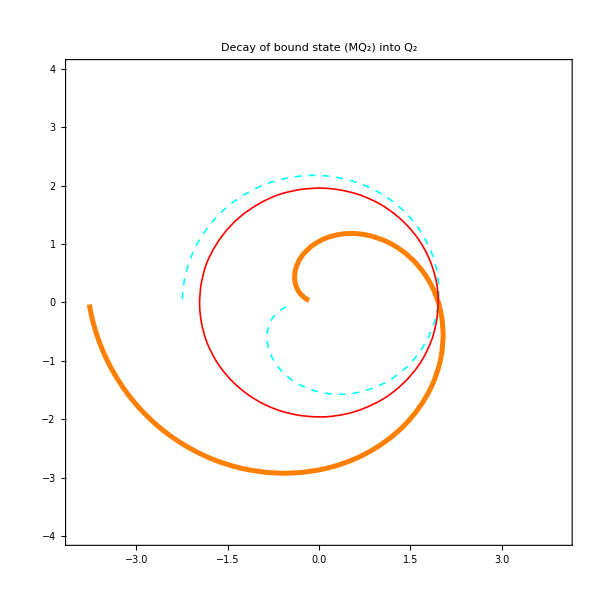

```mathematica
distance = 4;
c11 = ContourPlot[    Evaluate[  {  Im[  (top0[mz[x,y]] + ⅈ  0 quark1[mz[x,y]])/(ⅈ quark2[mz[x,y]])] == 0,
                                                            Abs[  top0[mz[x,y]] + ⅈ  0 quark1[mz[x,y]] ] == Abs[ quark2[mz[x,y]] ],
                                                            Abs[ mz[x, y] ] == 360^(1/3)} ], 
                             { x , -distance, distance},{y, -distance,distance},
                             ContourStyle->
                          { Directive[ Thickness[0.006], Orange ],  Directive[ Thickness[0.002], Cyan, Dashed ],   Directive[ Thickness[0.002],Red ] },
                             PlotLabel-> Style["Decay of bound state (MQ_2) into Q_2",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

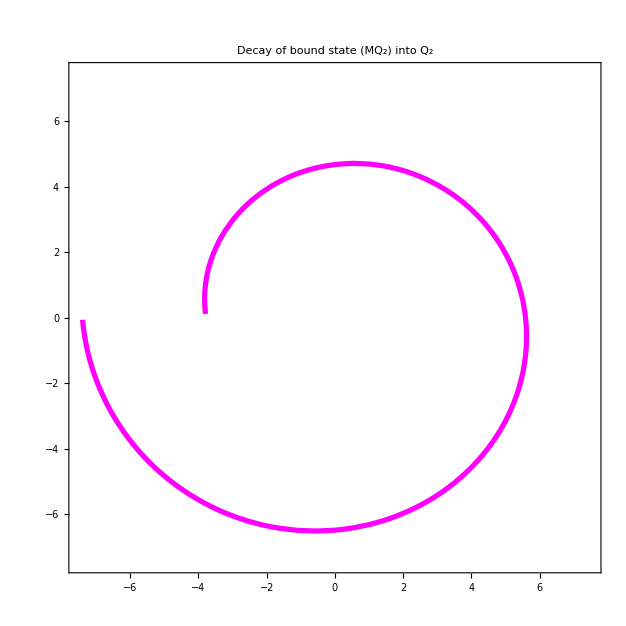

```mathematica
distance = 7.5;
c12 =ContourPlot[    Evaluate[  {    Im[  (top0[mz[x,y]] + ⅈ  ( -1) quark1[mz[x,y]])/(ⅈ quark2[mz[x,y]])] == 0} ], 
                             { x , -distance, distance},{y, -distance,distance},
                             ContourStyle->
                          { Directive[ Thickness[0.006], Magenta ] },
                             PlotLabel-> Style["Decay of bound state (MQ_2) into Q_2",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

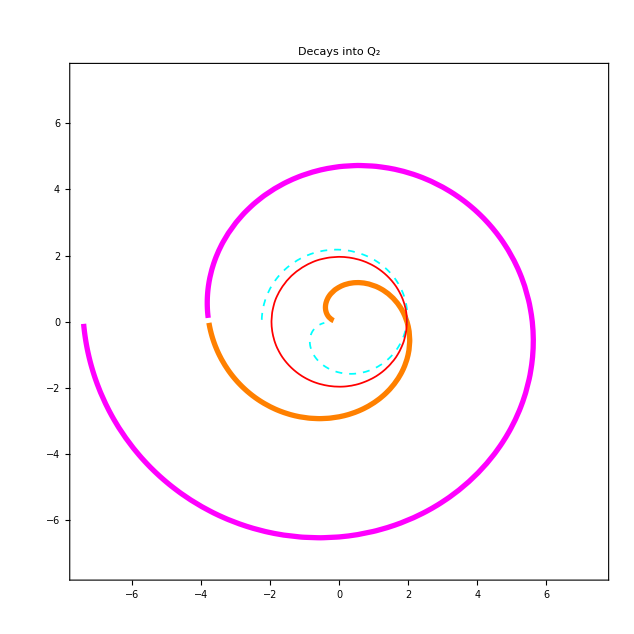

```mathematica
Show[c12,c11,  PlotLabel-> Style["Decays into Q_2",FontSize->24], LabelStyle->Directive[FontSize->18]]
```

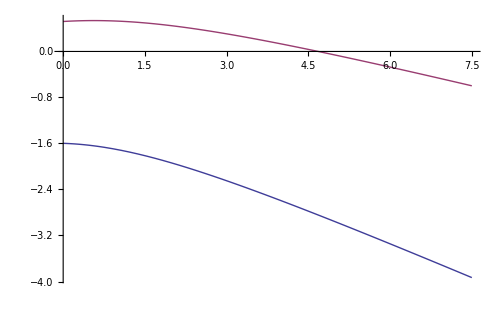

```mathematica
v= 2.5;
distance = 7.5;
Plot[  { Re[  (top0[mz[x,v]] + ⅈ  ( -1) quark1[mz[x,v]])/(ⅈ quark2[mz[x,v]])],Im[  (top0[mz[x,v]] + ⅈ  ( -1) quark1[mz[x,v]])/(ⅈ quark2[mz[x,v]])]  }, { x, 0, distance } ]
```

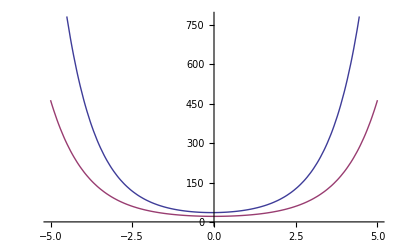

```mathematica
Plot[ { Abs [ top0[mz[x,v]] + ⅈ  ( -1) quark1[mz[x,v]] ], Abs [ quark2[mz[x,v]] ] }, { x, -5, 5} ]
```

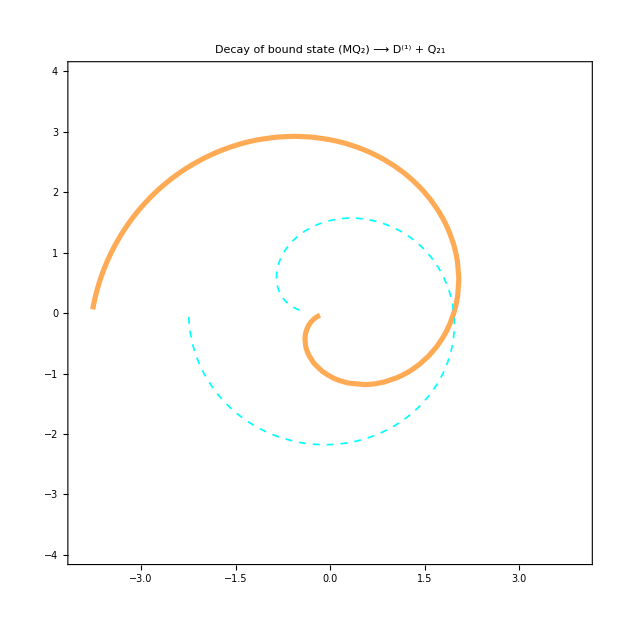

```mathematica
distance = 4.0;
c21 = ContourPlot[    Evaluate[  {  Im[  (top0[mz[x,y]] + ⅈ  1 quark1[mz[x,y]])/(ⅈ quark21[mz[x,y]])] == 0,
                                                             Abs[  top0[mz[x,y]] + ⅈ  1 quark1[mz[x,y]] ] == Abs[ quark21[mz[x,y]] ]} ], 
                             { x , -distance, distance},{y, -distance,distance},
                             ContourStyle->
                          { Directive[ Thickness[0.006], Lighter[Orange] ], Directive[ Thickness[0.002], Cyan, Dashed ]  },
                             PlotLabel-> Style["Decay of bound state (MQ_2) ⟶  D^(1) +  Q_21",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

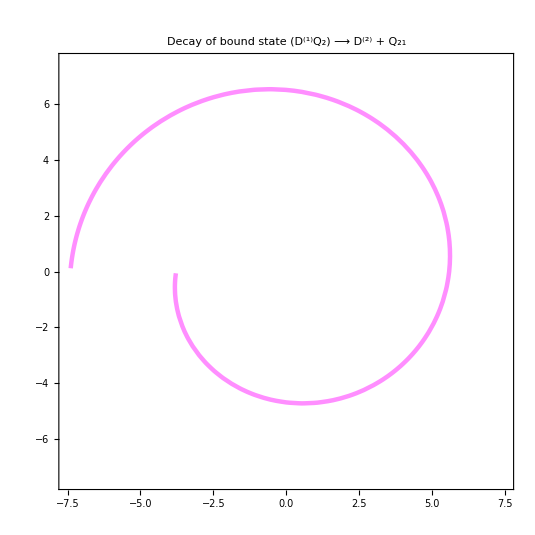

```mathematica
distance = 7.5;
c22 = ContourPlot[    Evaluate[  {  Im[  (top0[mz[x,y]] + ⅈ  2 quark1[mz[x,y]])/(ⅈ quark21[mz[x,y]])] == 0 } ], 
                             { x , -distance, distance},{y, -distance,distance},
                             ContourStyle->
                          { Directive[ Thickness[0.006], Lighter[Lighter[Magenta]] ] },
                             PlotLabel-> Style["Decay of bound state (D^(1)Q_2) ⟶  D^(2) +  Q_21",FontSize->24], LabelStyle->Directive[FontSize->18]   ]
```

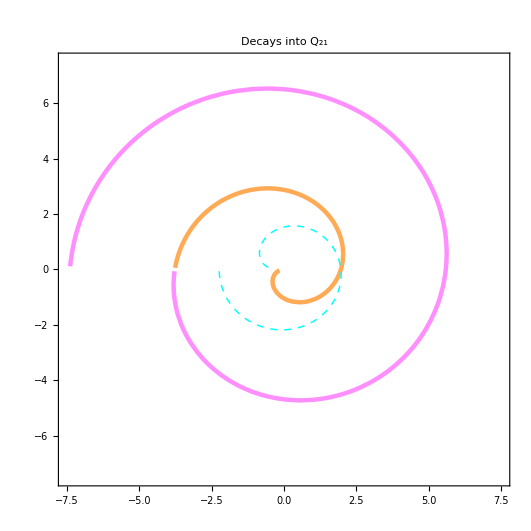

```mathematica
Show[c22,c21,  PlotLabel-> Style["Decays into Q_21",FontSize->24], LabelStyle->Directive[FontSize->18]]
```

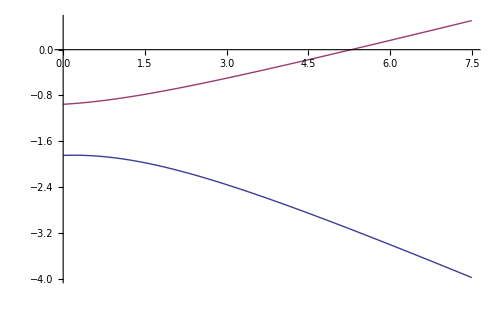

```mathematica
v= 2.5;
distance = 7.5;
Plot[  { Re[  (top0[mz[x,v]] + ⅈ  2 quark1[mz[x,v]])/(ⅈ quark21[mz[x,v]])],Im[  (top0[mz[x,v]] + ⅈ  2 quark1[mz[x,v]])/(ⅈ quark21[mz[x,v]])]  }, { x, 0, distance } ]
```

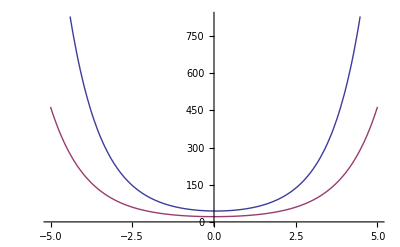

```mathematica
Plot[ { Abs [ top0[mz[x,v]] + ⅈ  2 quark1[mz[x,v]] ], Abs [ quark21[mz[x,v]] ] }, { x, -5, 5} ]
```

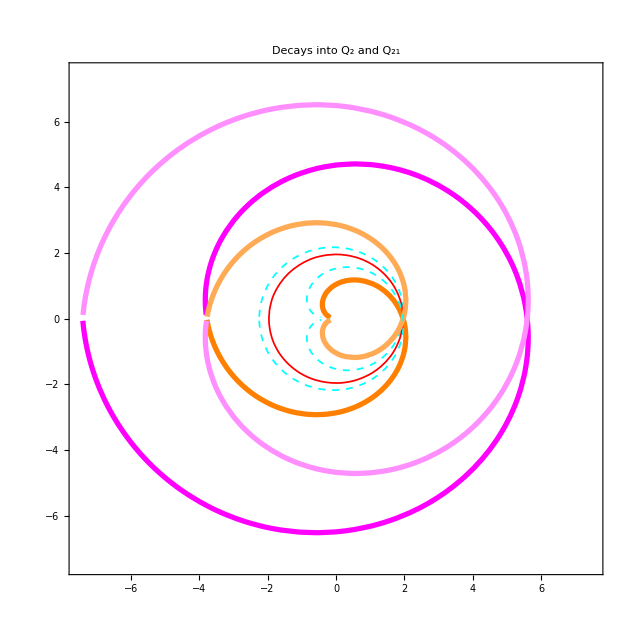

```mathematica
Show[c12,c11,c21,c22,  PlotLabel-> Style["Decays into Q_2 and Q_21",FontSize->24], LabelStyle->Directive[FontSize->18]]
```

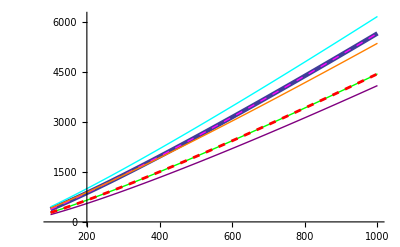

```mathematica
Plot[ { Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m0[m]], Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m1[m]], Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m0[m] - ⅈ quark1[m]],Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m2[m]],Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m2[m] + ⅈ quark1[m]], Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m2[m] - ⅈ quark1[m]],
Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m2[m] + ⅈ 2quark1[m]]} , {m, 100, 1000},
               PlotStyle->{ Directive[Thickness[0.008]], Directive[Magenta, Dashed], Directive[Cyan],Directive[Purple], Directive[Green], Directive[Red,Dashed,Thickness[0.005]],
                                       Directive[Orange] } ]
```

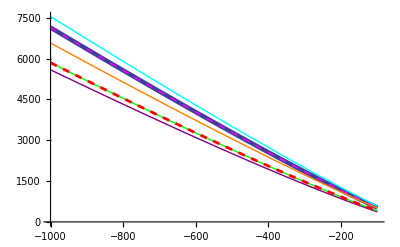

```mathematica
Plot[ { Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m0[m]], Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m1[m]], Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m0[m] - ⅈ quark1[m]],Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m2[m]],Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m2[m] + ⅈ quark1[m]], Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m2[m] - ⅈ quark1[m]],
Abs[( ⅇ^(2 π ⅈ / NN)  -   1 ) W0[m] + ⅈ m2[m] + ⅈ 2quark1[m]]} , {m, -1000, -100},
               PlotStyle->{ Directive[Thickness[0.008]], Directive[Magenta, Dashed], Directive[Cyan],Directive[Purple], Directive[Green], Directive[Red,Dashed,Thickness[0.005]],
                                       Directive[Orange] } ]
```